First note that without repressor interaction (ω=1) the possible logic functions are extremely limited:

```mathematica
Simplify[l[c1,c2,1],{c1>0,c2>0}]
```

1/2

This means than independent repressor binding can only generate SIG, SLOPE or asym-SLOPE logic. This could result in apparent AND logic if the repression by each was so strong as to lower it below background. We therefore focus on the solution to the interaction term ω and its relationship to logic and regulatory range.

```mathematica
ω[r_,a_,l_]:=(10^((a r)/2)+10^(1/2 (2+a) r)-10^(l r)-10^((a+l) r))/(10^((a r)/2)-10^(l r)-10^((a+l) r)+10^(1/2 (a+4 l) r))
```

To consider the case of symmetric repression, we take c1=c2=c, or equivalently, a=0. The logic is then given by:

```mathematica
l[c,c,ω]
```

Log[1+c]/Log[1+2 c+c^2 ω]

```mathematica
Log[1+c]/Log[1+2 c+c^2+c^2 (ω-1)]
```

From this function, it is clear that the most AND-like logic (largest l) for a given value of c ocurs when ω=0. Furthermore, as the repression coefficient c becomes very large, the logic becomes perfectly AND-like. Specifically, the best AND gates will have a large r.

```mathematica
Plot[l[c,c,0],{c,0,100},AxesLabel->{c,l}]
```

```mathematica
Limit[l[c,c,0],c->∞]
```

1

The logic function of a symmetric RR-promoter depends on the binding constant of the repressors, and their interaction parameter ω.

```mathematica
l[c,c,ω]
```

Log[1+c]/Log[1+2 c+c^2 ω]

We can  examine how AND-like the logic is for moderate levels of exclusive interaction.  As shown above, this function only becomes small for very large ω. For the case ω=1, we have l=1/2 independent of c.This implies that balanced independent repression always generates the SLOPE function.

```mathematica
Simplify[l[c,c,1],c>0]
```

1/2

```mathematica
ω[r,0,l]
```

(1-2^(1+l r) 5^(l r)+10^r)/(1-2^(1+l r) 5^(l r)+10^(2 l r))

In the case of balanced repression it is easy to calculate the repression constant and interaction term given the logic type and regulatory range. This function shows that an RR-promoter cannot generate OR logic becuase as a symmetric gate (a=0) becomes more OR-like (l→0), the necessary cooperativity explodes. This means that RR-promoters cannot generate symmetric OR logic. For example, for a 10-fold regulated OR gate:

```mathematica
Plot[ω[1,0,l],{l,0,1},AxesLabel->{l,ω}]
```

```mathematica
Limit[ω[1,0,l],l->0]
```

∞

What does ω look like as a function of r and l in a symmetric gate?

```mathematica
Plot3D[ω[r,0,l],{r,1,5},{l,0.1,1},AxesLabel->{r,l,ω},ColorFunction->Hue,Mesh->False,ViewPoint->{-18,-2,5}]
```

Again, that for a perfect OR gate (r >1 and l=0), we must have ω→∞. Furthermore, to get even a decent dual-repressor OR (r > 1, l < 0.1) we need to have an extremely strong cooperative interaction ω≈100.

How does ω behave as a function of a and l in a gate with fixed r?

```mathematica
Plot3D[ω[r,a,l]/.r->2,{a,0,0.9},{l,0.5,1},AxesLabel->{a,l,ω},ColorFunction->Hue,Mesh->False,ViewPoint->{18,12,5}]
```

Here we see that all AND-like logics are accesible with competitive interactions ω<1, the OR-like logics are accesible with cooperative interactions ω>1 (plot in progress...), and only SLOPE-like interactions are accesible with independent repression ω=1 (pink stripe).

Now consider the asymmetric logic gates where we fix the regulatory range. Then we can solve for ω in terms of the two repression constants and use this to determine (a,l) as a function of these constants.  Therefore, if we know the repression constants (i.e. from analysis of SIGs), then the interaction term will determine what types of logic are possible.

We can use these equations to examine the regions of allowed logical phenotype space as parametric curves. If we fix the range r and interaction ω terms, we can solve for a and l in terms of a single parameter: c1.  We can then examine the regions of phenotype space as parametric plots given fixed values of r and ω.

```mathematica
c2soln=Solve[r[c1,c2,ω]==r,c2]
```

{{c2→(-1+10^r-c1)/(1+c1 ω)}}

```mathematica
Simplify[a[c1,c2,ω]/.c2soln,r>0]
```

{(Log[1+c1]-Log[(10^r+c1 (-1+ω))/(1+c1 ω)])/(r Log[10])}

```mathematica
Simplify[l[c1,c2,ω]/.c2soln,r>0]
```

{(Log[1+c1]+Log[(10^r+c1 (-1+ω))/(1+c1 ω)])/(r Log[100])}

```mathematica
a[c1_,ω_,r_]:=(Log[1+c1]-Log[(10^r+c1 (-1+ω))/(1+c1 ω)])/(r Log[10])
l[c1_,ω_,r_]:=(Log[1+c1]+Log[(10^r+c1 (-1+ω))/(1+c1 ω)])/(r Log[100])
```

In order to examine the parametric plots, we must consider the minimum value of c1. In particular, c1 is always greater than c2, so for a given value of r and ω, c1 must be greater than:

```mathematica
Solve[r[c1,c1,ω]==r,c1]
```

{{c1→(-1-√(1-ω+10^r ω))/ω},{c1→(-1+√(1-ω+10^r ω))/ω}}

Only the positive root is physical, since the repression constant must be greater than zero (the negative root also explodes at ω=0). For the case of no interaction (ω=0), this expression reduces to:

```mathematica
Limit[(-1+√(1-ω+10^r ω))/ω,ω->0]
```

1/2 (-1+10^r)

So in the case of exclusive repression (ω=0), we see that the stronger repression coefficient c1 must increase proportionally with the regulatory range 10^r. Returning to the general case, the repression coefficient c1  for a fixed r and ω is greatest when it it completely dominant (c2 = 0). Thefore the maximum c1 is:

```mathematica
Solve[r[c1,0,ω]==r,c1]
```

{{c1→-1+10^r}}

```mathematica
ParametricPlot[{l[c1,0,1],a[c1,0,1]},{c1,9/2,9},AxesLabel->{l,a}]
```

For a simple 10-fold regulated gate with exclusive repression (r=1,ω=0), the allowed logic functions range from SIG (c1=9, c2=0) to almost AND-like (c1=c2=9/2). As we will see, to generate more AND-like logic we well need to examine the higher regulatory ranges.

Using the parametric solution, we can examine the allowed logics for multiple regulatory ranges and interaction paramters. It is clear  that the more AND-like logics ( l > 0.5) require competitive interaction ( ω < 1), whereas the more OR-like logics ( l < 0.5) require cooperative interaction ( ω > 1). Below we plot the allowed logics for 100-fold, 1000-fold, and 100,000-fold gates:

```mathematica
ParametricPlot[{{l[c1,0,r]/.r->2,a[c1,0,r]/.r->2},{l[c1,0.1,r]/.r->2,a[c1,0.1,r]/.r->2},{l[c1,1,r]/.r->2,a[c1,1,r]/.r->2},{l[c1,2,r]/.r->2,a[c1,2,r]/.r->2},{l[c1,20,r]/.r->2,a[c1,20,r]/.r->2}},{c1,Limit[(-1+√(1-ω+10^r ω))/ω,ω->20]/.r->2,-1+10^r/.r->2},AxesLabel->{l,a},PlotRange->{{0,1},{0,1}}]
```

```mathematica
ParametricPlot[{{l[c1,0,r]/.r->3,a[c1,0,r]/.r->3},{l[c1,0.01,r]/.r->3,a[c1,0.01,r]/.r->3},{l[c1,0.1,r]/.r->3,a[c1,0.1,r]/.r->3},{l[c1,1,r]/.r->3,a[c1,1,r]/.r->3},{l[c1,2,r]/.r->3,a[c1,2,r]/.r->3},{l[c1,20,r]/.r->3,a[c1,20,r]/.r->3}},{c1,Limit[(-1+√(1-ω+10^r ω))/ω,ω->20]/.r->3,-1+10^r/.r->3},AxesLabel->{l,a},PlotRange->{{0,1},{0,1}}]
```

```mathematica
ParametricPlot[{{l[c1,0,r]/.r->5,a[c1,0,r]/.r->5},{l[c1,0.001,r]/.r->5,a[c1,0.001,r]/.r->5},{l[c1,0.01,r]/.r->5,a[c1,0.01,r]/.r->5},{l[c1,0.1,r]/.r->5,a[c1,0.1,r]/.r->5},{l[c1,1,r]/.r->5,a[c1,1,r]/.r->5},{l[c1,2,r]/.r->5,a[c1,2,r]/.r->5},{l[c1,20,r]/.r->5,a[c1,20,r]/.r->5}},{c1,Limit[(-1+√(1-ω+10^r ω))/ω,ω->20]/.r->5,-1+10^r/.r->5},AxesLabel->{l,a},PlotRange->{{0,1},{0,1}}]
```

Clearly, the stronger the RR-promoter, the more AND-like we expect it to be. OR-like gates never occur, and the asym-OR gates face a trade-off between OR-ness and regulatory range, as well as requiring a strong cooperative interaction ( ω = 20 ).

It is also useful to solve for l in terms of r, a, and ω. This lets us examine the effect of the repression interaction on the type of logic found. We simply replace c1 and c2 with the equivalent expressions for (r,a,l)

```mathematica
c1soln=Solve[1/Log[r] Log[(1+c1)/(1+c2)]==a,c1]
```

{{c1→-1+r^a+c2 r^a}}

```mathematica
c2soln=Simplify[Solve[r==1+c1+c2+ω*c1*c2/.c1soln,c2]]
```

{{c2→(r^-a (-1-r^a+ω-r^a ω+√(4 r^a (r-r^a) ω+(1-ω+r^a (1+ω))^2)))/(2 ω)},{c2→-(r^-a (1+r^a-ω+r^a ω+√(4 r^a (r-r^a) ω+(1-ω+r^a (1+ω))^2)))/(2 ω)}}

```mathematica
Simplify[c1soln/.c2soln]
```

{{{c1→-(1+r^a+ω-r^a ω-√(4 r^a (r-r^a) ω+(1-ω+r^a (1+ω))^2))/(2 ω)}},{{c1→-(1+r^a+ω-r^a ω+√(4 r^a (r-r^a) ω+(1-ω+r^a (1+ω))^2))/(2 ω)}}}

```mathematica
l2[r_,a_,ω_]:=Simplify[l[-1/(2 ω)(1+r^a+ω-r^a ω-√(4 r^a (r-r^a) ω+(1-ω+r^a (1+ω))^2)),1/(2 ω)r^-a (-1-r^a+ω-r^a ω+√(4 r^a (r-r^a) ω+(1-ω+r^a (1+ω))^2)),ω]]
```

```mathematica
N[Limit[l2[1000,0,w],w->0]]
```

0.899801

```mathematica
ParametricPlot[{{l2[10000,a,100],a},{l2[10000,a,10],a},{l2[10000,a,1],a},{l2[10000,a,.1],a},{l2[10000,a,.01],a},{l2[10000,a,.001],a},{l2[10000,a,.0001],a},{l2[10000,a,.00001],a}},{a,0,1},PlotRange->{{0,1},{0,1}}]
```

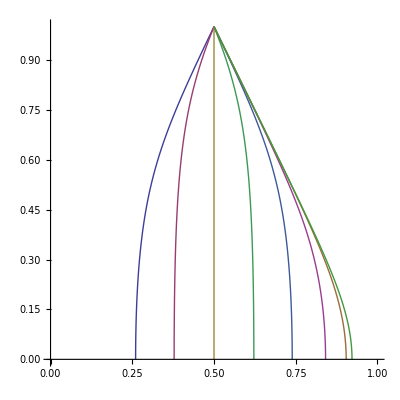

```mathematica
l2[r,a,ω]
```

1/(2 Log[r])(Log[(-1-r^a+ω+r^a ω+√(4 r^a (r-r^a) ω+(1-ω+r^a (1+ω))^2))/(2 ω)]+Log[(r^-a (-1-r^a+ω+r^a ω+√(4 r^a (r-r^a) ω+(1-ω+r^a (1+ω))^2)))/(2 ω)])